```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
f[x_]:=0;
σ[x_]:=0;
μ[x_]:=1;
n= 10;
h = 1.0/n;
g1 = InputFormAssistant;
β[x_]:= (-30*(10x-5)) /(1+(10x-5)^2);
```

```mathematica
"2.      Знайти апроксимацію розв’язку з допомогою вбудованих функцій NDSolve/NDSolveValue"
eqn =- D[μ[x]* D[u[x], x], x] +β[x]* D[u[x], x] + σ[x]* u[x] +NeumannValue[InputFormAssistant, x == 1]  == f[x];
boundaryConditions = {DirichletCondition[u[x] == 1, x == 0]};
solution = NDSolveValue[{eqn, boundaryConditions}, u, {x, 0, 1}];
Print [solution];
Plot[solution[x], {x, 0, 1}, PlotRange -> All, AxesLabel -> {"x", "u(x)"}]
```

2.      Знайти апроксимацію розв’язку з допомогою вбудованих функцій NDSolve/NDSolveValue

InterpolatingFunction[…]

-Graphics-

```mathematica
improvedFEMImplementation[n_,xvals_, h_]:=Module[{A,l,j,xm, xM},
A=Table[0,{j,0,n},{i,0,n}];
l=Table[0, {j,0,n}];

l[[1]]= 1;(*діріхле*)
A[[1,1]]=1;
A[[1,2]] = 0;   
For[j=1,j <n,j++,
xm = InputFormAssistant;
xM = InputFormAssistant;
A[[j+1,j]]=μ[xm]*(InputFormAssistant)+β[xm]*(InputFormAssistant)+σ[xm]InputFormAssistant;
A[[j+1,j+1]]=μ[xm]InputFormAssistant+β[xm]InputFormAssistant+σ[xm]InputFormAssistant + μ[xM]InputFormAssistant+β[xM]*(InputFormAssistant)+σ[xM]InputFormAssistant ;
A[[j+1,j+2]]=μ[xM]*(InputFormAssistant)+β[xM]InputFormAssistant+σ[xM]InputFormAssistant;
l[[j+1]] = f[xm]InputFormAssistant+f[xM]InputFormAssistant;

];
xm=InputFormAssistant;
l[[n+1]]= f[xm]InputFormAssistant-g1;
A[[n+1, n]]=μ[xm]*(InputFormAssistant)+β[xm]*(InputFormAssistant)+σ[xm]InputFormAssistant;
A[[n+1, n+1]]=μ[xm]*(InputFormAssistant)+β[xm]*(InputFormAssistant)+σ[xm]InputFormAssistant;
Return[{N[A],N[l]}];
];
```

```mathematica
"1.      Знайти апроксимацію розв'язку Методом Скінченних Елементів"
xvals=Table[j/n,{j,0,n}];
{A,l}=improvedFEMImplementation[n,xvals, h ];
uvals=LinearSolve[A,l];
(*A // MatrixForm
l // MatrixForm
Print[uvals];
Print[xvals];*)
ListPlot[Transpose[{xvals,uvals}]]
```

1.      Знайти апроксимацію розв'язку Методом Скінченних Елементів

-Graphics-

```mathematica
"3. Обчислити наступні оцінювачі похибок апроксимацій:"
"4. Вивести графіки розподілу оцінювачів похибки по скінченних елементах"
"a. Явний оцінювач похибки (нев’язку диф. Рівняння)"
un=Interpolation[Transpose[{xvals,uvals}]];
Print["\"∥\!\(\*SubscriptBox[\(u\), \(n\)]\)\!\(\*SuperscriptBox[\(∥\), \(2\)]\)=∫...dx=\"",Round[NIntegrate[un'[x]^2+un[x]^2,{x,0,1}],0.0001]]
Print["\"∥u\!\(\*SuperscriptBox[\(∥\), \(2\)]\)=∫...dx=\"",Round[NIntegrate[D[InputFormAssistant,x]+ InputFormAssistant,{x,0,1}],0.0001]]
calcExplicitError[α_, n_,h_]:=Module[{r=Table[0,Length[α]-1],i,xs},
For[i=1,i≤n,++i,
xs=Mean[xvals[[{i,i+1}]]];
r[[i]]=h^2(f[xs]-α[[{i,i+1}]].((β[xs]-μ'[xs])/h{-1,1}+σ[xs]/2{1,1}))^2
];
Return[r];
];

ListPlot[{calcExplicitError[uvals,n,h], calcExplicitError[solution[xvals],n,h]}]
Print["\"r(\!\(\*SubscriptBox[\(u\), \(n\)]\)\!\(\*SuperscriptBox[\()\), \(2\)]\)=\"",Round[Total[calcExplicitError[uvals,n,h]],0.0001]]
Print["\"r(u\!\(\*SuperscriptBox[\()\), \(2\)]\)=\"",Round[Total[calcExplicitError[solution[xvals],n,h]],0.0001]]
```

3. Обчислити наступні оцінювачі похибок апроксимацій:

4. Вивести графіки розподілу оцінювачів похибки по скінченних елементах

a. Явний оцінювач похибки (нев’язку диф. Рівняння)

"∥u_n∥^2=∫...dx="18.2961

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.550766}. NIntegrate obtained 5.43928 and 0.000507584 for the integral and error estimates.

"∥u∥^2=∫...dx="5.4393

-Graphics-

"r(u_n)^2="189.879

"r(u)^2="41.1264

```mathematica
"b. Стрибок градієнта"
leftBC= "Dirichlet";
rightBC = "Neuman";     
leftG =0;
leftQ=0;
rightG=  InputFormAssistant;
rightQ=0;
jump[solution_, n_,h_] := Module[
  { x, JumpList, rightX, leftX, rightAlpha, leftAlpha, i, diffFI
  },
    diffFI = {-1, 1};
    
 xvals = Table[j/n,{j,0,n}];
 
  
  JumpList = Table[0, {n}];
  If[leftBC === "Robin"|| leftBC === "Neuman",
    rightX = xvals[[1]] + h / 2;
    rightAlpha = {solution[[1]], solution[[2]]};
    JumpList[[1]] = h^2 (μ[rightX] Dot[rightAlpha, diffFI] - (leftG - leftQ solution[[1]]));
  ];
  
  For[i = 2, i ≤ n - 1, i++,
    rightX = xvals[[i]] + h / 2;
    leftX = xvals[[i]] - h / 2;
    rightAlpha = {solution[[i]], solution[[i + 1]]};
    leftAlpha = {solution[[i - 1]], solution[[i]]};
    JumpList[[i]] = h^2 (μ[rightX]Dot[rightAlpha, diffFI] - μ[leftX] Dot[leftAlpha, diffFI])^2;
  ];
  If[rightBC === "Robin"  || rightBC === "Neuman"  ,
    leftX = xvals[[-1]] - h / 2;
    leftAlpha = {solution[[-2]], solution[[-1]]};
    JumpList[[-1]] = h^2 (rightG - rightQ solution[[-1]] - μ[leftX] Dot[leftAlpha, diffFI]);
  ];
  
  Return[JumpList]
]
```

b. Стрибок градієнта

```mathematica
Print[jump[uvals,n,h]];
ListPlot[{jump[uvals,n,h],jump[solution[xvals],n,h]}]
Print["\"j(\!\(\*SubscriptBox[\(u\), \(n\)]\)\!\(\*SuperscriptBox[\()\), \(2\)]\)=\"",Round[Total[jump[uvals,n,h]],0.0001]]
Print["\"(j\!\(\*SuperscriptBox[\()\), \(2\)]\)=\"",Round[Total[jump[solution[xvals],n,h]],0.0001]]
```

{0,4.93924×10^-7,6.02479×10^-6,0.000217511,0.00357236,0.,0.00357236,0.000217511,6.02479×10^-6,-0.000444056}

-Graphics-

"j(u_n)^2="0.0071

"(j)^2="0.0011

```mathematica
"c. Неявний оцінювач Діріхле"
calcImplicitDirichlet[α_ ,n_,h_]:=Module[{r=Table[0,Length[α]-1],i,xs},
For[i=1,i≤n,++i,
xs=Mean[xvals[[{i,i+1}]]];
r[[i]]=h^2(f[xs]-α[[{i,i+1}]].((β[xs]-μ'[xs])/h{-1,1}+σ[xs]/2{1,1}))^2;
r[[i]]/=(6/5 μ[xs]/h(10+h^2 σ[xs]/μ[xs]));
];
Return[N[r]];
];

ListPlot[{calcImplicitDirichlet[uvals, n,h], calcImplicitDirichlet[solution[xvals], n,h]}]
Print["\"ImplicitDirichlet(\!\(\*SubscriptBox[\(u\), \(n\)]\)\!\(\*SuperscriptBox[\()\), \(2\)]\)=\"",Round[Total[calcImplicitDirichlet[uvals, n,h]],0.0001]]
Print["\"ImplicitDirichlet(u\!\(\*SuperscriptBox[\()\), \(2\)]\)=\"",Round[Total[calcImplicitDirichlet[solution[xvals], n,h]],0.0001]]
```

c. Неявний оцінювач Діріхле

-Graphics-

"ImplicitDirichlet(u_n)^2="1.5823

"ImplicitDirichlet(u)^2="0.3427

```mathematica
"d. Неявний оцінювач Неймана"
calcImplicitNeumann[α_,n_, h_]:=Module[{r=Table[0,Length[α]-1],i,xs},
For[i=1,i≤n,++i,
xs=Mean[xvals[[{i,i+1}]]];
r[[i]]=h^2(f[xs]-α[[{i,i+1}]].((β[xs]-μ'[xs])/h{-1,1}+σ[xs]/2{1,1}))^2;
r[[i]]/=(InputFormAssistant μ[xs]/h(12+h^2 σ[xs]/μ[xs]));
];
Return[r];
];
ListPlot[{calcImplicitNeumann[uvals, n,h], calcImplicitNeumann[solution[xvals], n,h]}]
Print["\"ImplicitNeumann(\!\(\*SubscriptBox[\(u\), \(n\)]\)\!\(\*SuperscriptBox[\()\), \(2\)]\)=\"",Round[Total[calcImplicitNeumann[uvals, n,h]],0.0001]]
Print["\"ImplicitNeumann(u\!\(\*SuperscriptBox[\()\), \(2\)]\)=\"",Round[Total[calcImplicitNeumann[solution[xvals], n,h]],0.0001]]
```

d. Неявний оцінювач Неймана

-Graphics-

"ImplicitNeumann(u_n)^2="1.1867

"ImplicitNeumann(u)^2="0.257

```mathematica
(*5Виконати описані вище кроки для різної кількості скінченних елементів 
6Починаючи з n=4 та збільшуючи кількість скінченних елементів вдвічі на кожній ітерації знайти таке N при якому різниця по модулю стрибка градієнту між двома ітераціями менша ніж 10^(-4). 
7Вивести табличку, де кожен рядок відповідає певній ітерації, яка містить наступні значення: кіль-сть скінченних елементів, та усіх оцінювачів похибки. 
8Вивести графік значень усіх оцінювачів для усіх ітерацій *)
"Деякі графіки що повторюються з попередньою роботою я не виводжу щоб не вийти за можливіть по пам'яті вольфраму "


nincrement=4;
prevJump=0;
Jump=0;
JumpList={};
ExplicitError=0;
ExplicitErrorList={};
ImplicitDirichlet =0;
ImplicitDirichletList={};
ImplicitNeumann = 0;
ImplicitNeumannList ={};
nevuaskaList ={};
table = {};
JumpList={};
energyNormsList={};
xlist={};
While [True,
xvalsi=Table[InputFormAssistant,{j,0,nincrement}];
{A,l}=improvedFEMImplementation[nincrement,xvalsi,1/nincrement ];
uvalsi=LinearSolve[A,l];
Jump=jump[uvalsi,nincrement,1/nincrement];
Print [Length[Jump]];
ExplicitError=calcExplicitError[uvalsi,nincrement,1/nincrement];
ImplicitDirichlet=calcImplicitDirichlet[uvalsi,nincrement,1/nincrement];
ImplicitNeumann = calcImplicitNeumann[uvalsi,nincrement,1/nincrement];

JumpT=Round[Total[Jump]/nincrement,0.00001];
ExplicitErrorT=Round[Total[ExplicitError]/nincrement,0.00001];
ImplicitDirichletT=Round[Total[ImplicitDirichlet]/nincrement,0.00001];
ImplicitNeumannT=Round[Total[ImplicitNeumann]/nincrement,0.00001];
un=Interpolation[Transpose[{xvalsi,uvalsi}]];
nevuaska=Round[NIntegrate[un'[x]^2+un[x]^2,{x,0,1}],0.0001];
nevuaskaT =nevuaska/nincrement;

Print["Iteration ",Length[table],": N =",nincrement,", Gradient Jamp =",JumpT,", ExplicitError =",ExplicitErrorT,", ImplicitDirichlet =",ImplicitDirichletT,", ImplicitNeumann =",ImplicitNeumannT,", \"∥\!\(\*SubscriptBox[\(u\), \(n\)]\)\!\(\*SuperscriptBox[\(∥\), \(2\)]\)=∫...dx=\"",nevuaskaT];

Bar=BarChart[Transpose[{JumpT,ExplicitErrorT,ImplicitDirichletT,ImplicitNeumannT,nevuaskaT}],ChartLabels->{"Gradient Jamp","ExplicitError","ImplicitDirichlet","ImplicitNeumann","\"∥\!\(\*SubscriptBox[\(u\), \(n\)]\)\!\(\*SuperscriptBox[\(∥\), \(2\)]\)=∫...dx=\""},PlotLabel->"Errors",Frame->True,FrameLabel->{"Iteration","Errors Value"}];

AppendTo[table,{nincrement,JumpT,ExplicitErrorT,ImplicitDirichletT, ImplicitNeumannT,nevuaskaT,Bar}];
AppendTo[JumpList,Jump];
AppendTo[ExplicitErrorList,ExplicitError];
AppendTo[ImplicitDirichletList,ImplicitDirichlet];
AppendTo[ImplicitNeumannList,ImplicitNeumann];
AppendTo[nevuaskaList,nevuaska];
AppendTo[xlist,Table[InputFormAssistant,{j,0,nincrement-1}]];
If[Abs[JumpT-prevJump]<10^-4,Break[]];
prevJump=JumpT;
nincrement*=2;
];
```

Деякі графіки що повторюються з попередньою роботою я не виводжу щоб не вийти за можливіть по пам'яті вольфраму

4

Iteration 0: N =4, Gradient Jamp =0.0001, ExplicitError =0.65655, ImplicitDirichlet =0.01368, ImplicitNeumann =0.01026, "∥u_n∥^2=∫...dx="0.2922

8

Iteration 1: N =8, Gradient Jamp =0.01566, ExplicitError =220.51, ImplicitDirichlet =2.29697, ImplicitNeumann =1.72273, "∥u_n∥^2=∫...dx="12.1667

16

Iteration 2: N =16, Gradient Jamp =0.00001, ExplicitError =1.93927, ImplicitDirichlet =0.0101, ImplicitNeumann =0.00758, "∥u_n∥^2=∫...dx="0.483119

32

Iteration 3: N =32, Gradient Jamp =0., ExplicitError =0.3159, ImplicitDirichlet =0.00082, ImplicitNeumann =0.00062, "∥u_n∥^2=∫...dx="0.185413

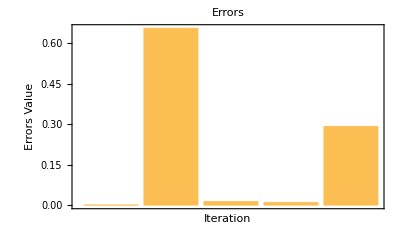
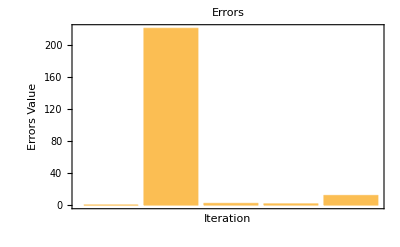
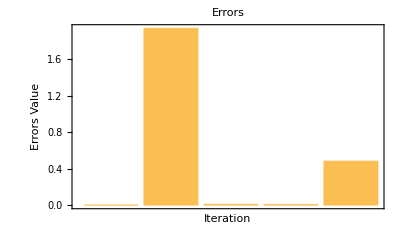
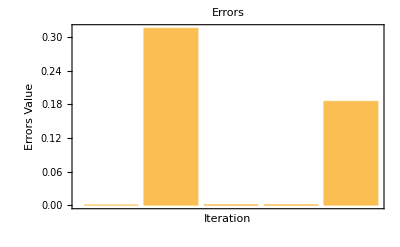
Number of Elements (N) | Gradient Jamp | ExplicitError | ImplicitDirichlet | ImplicitNeumann | "∥u_n∥^2=∫...dx=" | Plot
4 | 0.0001 | 0.65655 | 0.01368 | 0.01026 | 0.2922 | -Graphics-
8 | 0.01566 | 220.51 | 2.29697 | 1.72273 | 12.1667 | -Graphics-
16 | 0.00001 | 1.93927 | 0.0101 | 0.00758 | 0.483119 | -Graphics-
32 | 0. | 0.3159 | 0.00082 | 0.00062 | 0.185413 | -Graphics-

```mathematica
TableForm[table,TableHeadings->{None,{"Number of Elements (N)","Gradient Jamp","ExplicitError","ImplicitDirichlet","ImplicitNeumann","\"∥\!\(\*SubscriptBox[\(u\), \(n\)]\)\!\(\*SuperscriptBox[\(∥\), \(2\)]\)=∫...dx=\"", "Plot"}}]
```

```mathematica
"розподілу оцінювачів похибки по скінченних елементах по ітераціях"
```

розподілу оцінювачів похибки по скінченних елементах по ітераціях

```mathematica
n=4;
For[ i =1, i≤6, i++,
xvals=Table[j/n,{j,0,n}];
{A,l}=improvedFEMImplementation[n,xvals, h ];
uvals=LinearSolve[A,l];
un=Interpolation[Transpose[{xvals,uvals}]];
Print["Iteration :",i ,"   N = ",n]; 
Print["\"∥\!\(\*SubscriptBox[\(u\), \(n\)]\)\!\(\*SuperscriptBox[\(∥\), \(2\)]\)=∫...dx=\"",Round[NIntegrate[un'[x]^2+un[x]^2,{x,0,1}],0.0001]]
Print["\"∥u\!\(\*SuperscriptBox[\(∥\), \(2\)]\)=∫...dx=\"",Round[NIntegrate[D[InputFormAssistant,x]+ InputFormAssistant,{x,0,1}],0.0001]]
Print[ListPlot[{calcExplicitError[uvals,n,h], calcExplicitError[solution[xvals],n,h]},PlotLabel->"ExplicitError"]]
Print["\"r(\!\(\*SubscriptBox[\(u\), \(n\)]\)\!\(\*SuperscriptBox[\()\), \(2\)]\)=\"",Round[Total[calcExplicitError[uvals,n,h]],0.0001]]
Print["\"r(u\!\(\*SuperscriptBox[\()\), \(2\)]\)=\"",Round[Total[calcExplicitError[solution[xvals],n,h]],0.0001]]
Print[ListPlot[{jump[uvals,n,h],jump[solution[xvals],n,h]},PlotLabel->"Jump"]]
Print["\"j(\!\(\*SubscriptBox[\(u\), \(n\)]\)\!\(\*SuperscriptBox[\()\), \(2\)]\)=\"",Round[Total[jump[uvals,n,h]],0.0001]]
Print["\"(j\!\(\*SuperscriptBox[\()\), \(2\)]\)=\"",Round[Total[jump[solution[xvals],n,h]],0.0001]]
Print[ListPlot[{calcImplicitDirichlet[uvals, n,h], calcImplicitDirichlet[solution[xvals], n,h]},PlotLabel->"ImplicitDirichlet"]]
Print["\"ImplicitDirichlet(\!\(\*SubscriptBox[\(u\), \(n\)]\)\!\(\*SuperscriptBox[\()\), \(2\)]\)=\"",Round[Total[calcImplicitDirichlet[uvals, n,h]],0.0001]]
Print["\"ImplicitDirichlet(u\!\(\*SuperscriptBox[\()\), \(2\)]\)=\"",Round[Total[calcImplicitDirichlet[solution[xvals], n,h]],0.0001]]
Print[ListPlot[{calcImplicitNeumann[uvals, n,h], calcImplicitNeumann[solution[xvals], n,h]},PlotLabel->"ImplicitDirichlet"]]
Print["\"ImplicitNeumann(\!\(\*SubscriptBox[\(u\), \(n\)]\)\!\(\*SuperscriptBox[\()\), \(2\)]\)=\"",Round[Total[calcImplicitNeumann[uvals, n,h]],0.0001]]
Print["\"ImplicitNeumann(u\!\(\*SuperscriptBox[\()\), \(2\)]\)=\"",Round[Total[calcImplicitNeumann[solution[xvals], n,h]],0.0001]]
n++;
];
```

Iteration :1   N = 4

"∥u_n∥^2=∫...dx="1.117

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.550766}. NIntegrate obtained 5.43928 and 0.000507584 for the integral and error estimates.

"∥u∥^2=∫...dx="5.4393

-Graphics-

"r(u_n)^2="0.7195

"r(u)^2="96.0828

-Graphics-

"j(u_n)^2="-0.0005

"(j)^2="0.0013

-Graphics-

"ImplicitDirichlet(u_n)^2="0.006

"ImplicitDirichlet(u)^2="0.8007

-Graphics-

"ImplicitNeumann(u_n)^2="0.0045

"ImplicitNeumann(u)^2="0.6005

Iteration :2   N = 5

"∥u_n∥^2=∫...dx="1.1167

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.550766}. NIntegrate obtained 5.43928 and 0.000507584 for the integral and error estimates.

"∥u∥^2=∫...dx="5.4393

-Graphics-

"r(u_n)^2="0.166

"r(u)^2="4.3931

-Graphics-

"j(u_n)^2="-0.0004

"(j)^2="0.0067

-Graphics-

"ImplicitDirichlet(u_n)^2="0.0014

"ImplicitDirichlet(u)^2="0.0366

-Graphics-

"ImplicitNeumann(u_n)^2="0.001

"ImplicitNeumann(u)^2="0.0275

Iteration :3   N = 6

"∥u_n∥^2=∫...dx="1.4306

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.550766}. NIntegrate obtained 5.43928 and 0.000507584 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

"∥u∥^2=∫...dx="5.4393

-Graphics-

"r(u_n)^2="4.8935

"r(u)^2="83.7816

-Graphics-

"j(u_n)^2="-0.0003

"(j)^2="0.0025

-Graphics-

"ImplicitDirichlet(u_n)^2="0.0408

"ImplicitDirichlet(u)^2="0.6982

-Graphics-

"ImplicitNeumann(u_n)^2="0.0306

"ImplicitNeumann(u)^2="0.5236

Iteration :4   N = 7

"∥u_n∥^2=∫...dx="1.6017

"∥u∥^2=∫...dx="5.4393

-Graphics-

"r(u_n)^2="2.4855

"r(u)^2="11.0552

-Graphics-

"j(u_n)^2="-0.0003

"(j)^2="0.0036

-Graphics-

"ImplicitDirichlet(u_n)^2="0.0207

"ImplicitDirichlet(u)^2="0.0921

-Graphics-

"ImplicitNeumann(u_n)^2="0.0155

"ImplicitNeumann(u)^2="0.0691

Iteration :5   N = 8

"∥u_n∥^2=∫...dx="3.1958

"∥u∥^2=∫...dx="5.4393

-Graphics-

"r(u_n)^2="28.1141

"r(u)^2="59.4859

-Graphics-

"j(u_n)^2="0.0005

"(j)^2="0.0017

-Graphics-

"ImplicitDirichlet(u_n)^2="0.2343

"ImplicitDirichlet(u)^2="0.4957

-Graphics-

"ImplicitNeumann(u_n)^2="0.1757

"ImplicitNeumann(u)^2="0.3718

Iteration :6   N = 9

"∥u_n∥^2=∫...dx="6.0956

"∥u∥^2=∫...dx="5.4393

-Graphics-

"r(u_n)^2="32.5516

"r(u)^2="16.4964

-Graphics-

"j(u_n)^2="0.0014

"(j)^2="0.0019

-Graphics-

"ImplicitDirichlet(u_n)^2="0.2713

"ImplicitDirichlet(u)^2="0.1375

-Graphics-

"ImplicitNeumann(u_n)^2="0.2034

"ImplicitNeumann(u)^2="0.1031